```mathematica
data30=Import["F:\\SKF\\pku\\大三上\\计算物理学（B）\\作业\\1.5\\python\\output30.txt","list"];data30nr=Import["F:\\SKF\\pku\\大三上\\计算物理学（B）\\作业\\1.5\\python\\output30_no_resistance.txt","list"];
data40=Import["F:\\SKF\\pku\\大三上\\计算物理学（B）\\作业\\1.5\\python\\output40.txt","list"];data40nr=Import["F:\\SKF\\pku\\大三上\\计算物理学（B）\\作业\\1.5\\python\\output40_no_resistance.txt","list"];
data50=Import["F:\\SKF\\pku\\大三上\\计算物理学（B）\\作业\\1.5\\python\\output50.txt","list"];data50nr=Import["F:\\SKF\\pku\\大三上\\计算物理学（B）\\作业\\1.5\\python\\output50_no_resistance.txt","list"];
data={data30,data30nr,data40,data40nr,data50,data50nr};
points=Table[Table[{data[[j,i]],data[[j,i+1]]},{i,1,Length[data[[j]]],5}],{j,1,6,2}];pointsnr=Table[Table[{data[[j,i]],data[[j,i+1]]},{i,1,Length[data[[j]]],5}],{j,2,6,2}];
```

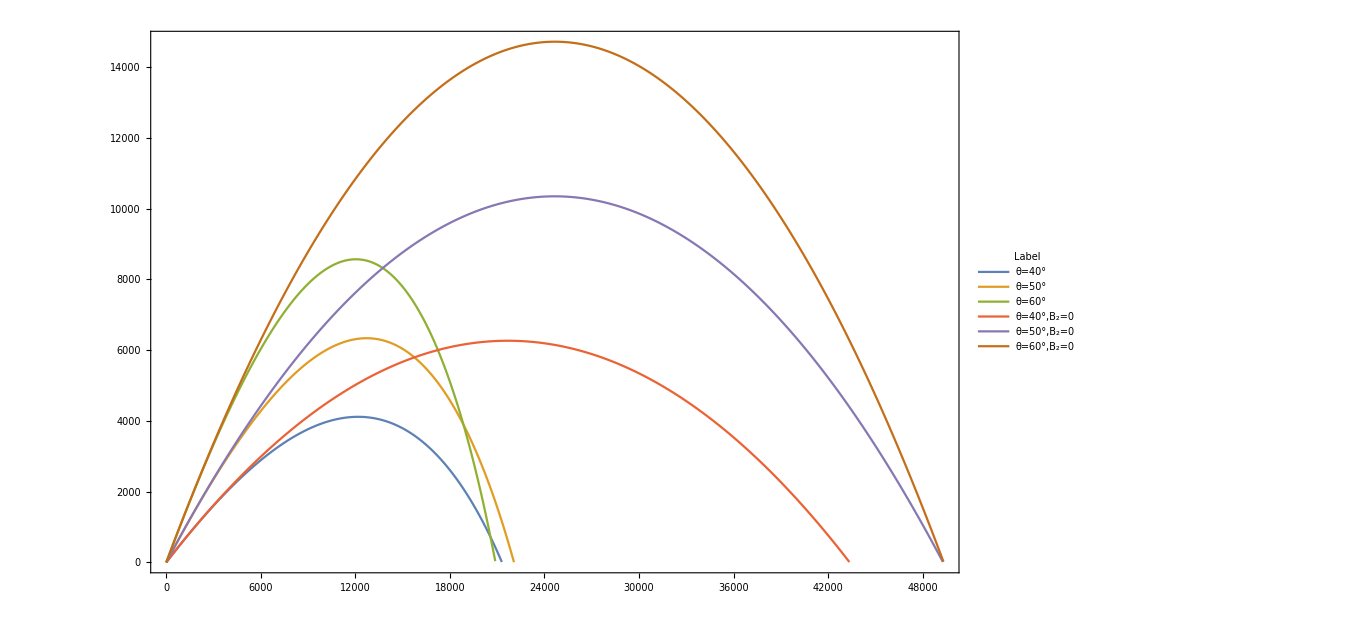

```mathematica
ListLinePlot[Join[points,pointsnr],Frame->True,Mesh->{{},{0}},PlotLegends->Placed[LineLegend[{"θ=40°","θ=50°","θ=60°","θ=40°,B_2=0","θ=50°,B_2=0","θ=60°,B_2=0"},LegendLabel->"Label",LegendFunction->(Framed[#,Background->LightBlue]&)],{0.9,0.8}]]
```